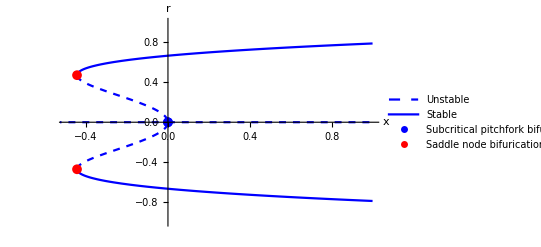

```mathematica
(*2a*)
(*Make a bifurcation diagram of x* vs r using dotted lines to indicate unstable fixed points and solid lines to indicate stable fixed points. Identify the different bifurcations and label them in the plot*)

ClearAll["Global`*"];
Remove["Global`*"]
SetOptions[$FrontEnd,ShowCellLabel->False]
f[x] := r*x+4*x^3-9*x^5;
xsolution = Solve[f[x]==0,x];
x=xsolution[[All,1,2]];
p = Plot[x,{r,-0.5,0.5}];
(*Bifurcation points*)
limits=FunctionDomain[x,{r}];
xLimitsMin=x/. r->limits[[1]];
xLimitsMax=x/. r->limits[[5]];
(*By using the plot and the point we can find the bifurcation points*)bifurcationP=List[{limits[[5]],xLimitsMax[[1]]},{limits[[1]],xLimitsMin[[2]]},{limits[[1]],xLimitsMin[[3]]}];
(*Final plot*)
p1 = Plot[x[[1]],{r,-1,0}, PlotStyle->{Blue, Dashed},PlotLegends->{"Unstable"}];
p2 = Plot[x[[1]],{r,0,1}, PlotStyle->{Blue, Dashed}];
p3 = Plot[x[[2]],{r,-1,1}, PlotStyle->{Blue, Dashed}];
p4=Plot[x⟦3⟧,{r,-1,1},PlotStyle->{{Blue,Dashed},Blue}];p5=Plot[x⟦4⟧,{r,-1,1},PlotStyle->Blue,PlotLegends->{"Stable"}];
p6=Plot[x⟦5⟧,{r,-1,1},PlotStyle->Blue];
p7=ListPlot[{bifurcationP[[1]]},PlotMarkers->{Automatic,10},PlotStyle->Blue,PlotLegends->{"Subcritical pitchfork bifurcation"}];p8=ListPlot[{bifurcationP[[2]],bifurcationP[[3]]},PlotMarkers->{Automatic,10},PlotStyle->Red,PlotLegends->{"Saddle node bifurication"}];p9 = Show[p1,p2,p3,p4,p5,p6,p7,p8,Axes->{True,True},AxesLabel->{"x","r"},PlotRange->{{-0.5,1},{-1,1}}]
Export["1.2a_plot.png",p9]
```

```mathematica
(*1.2b*)
(*Find two saddle-node bifurcations. Analytically calculate the point rc
​​ where these occur*)
(*To find the r_c point we can look at the bifurcation diagram and for r=rc we can see that rc is the point on the negative x-axis*)
rc=limits[[1]];
```

-4/9